```mathematica
a0=-7.803*10^-1
a1=1
a2=-2.886*10^-1
a4=8.130*10^-3
a6=-2.004*10^-4
a8=3.625*10^-6
a10=-4.969*10^-8
a12=5.339*10^-10
a14=-4.655*10^-12
```

-0.7803

1

-0.2886

0.00813

-0.0002004

3.625×10^-6

-4.969×10^-8

5.339×10^-10

-4.655×10^-12

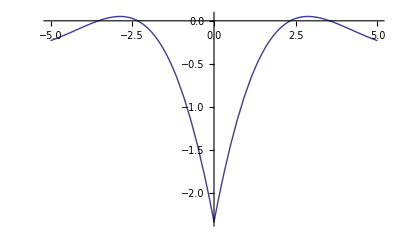

```mathematica
an=Plot[(-0.862+Abs[x/t]+2/(3*π)*∑_(n=1)^100 ((-1)^n Gamma[(2*n-1)/3])/Factorial[(2*n)]*Abs[x/t]^(2*n))*t+(a0+a1*Abs[x/t]+a2*Abs[x/t]^2+a4*Abs[x/t]^4+a6*Abs[x/t]^6+a8*Abs[x/t]^8+a10*Abs[x/t]^10+a12*Abs[x/t]^12+a14*Abs[x/t]^14)*t-0.3*t,{x,-5,5}]
```

```mathematica
Export["B3D.avi",an]
```

B3D.avi

1

1.5

2

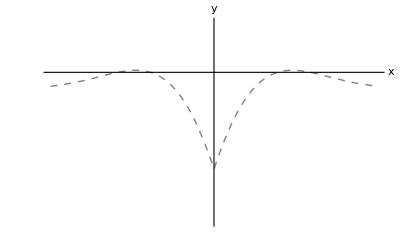

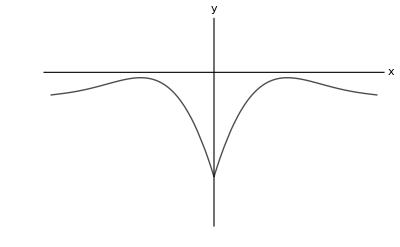

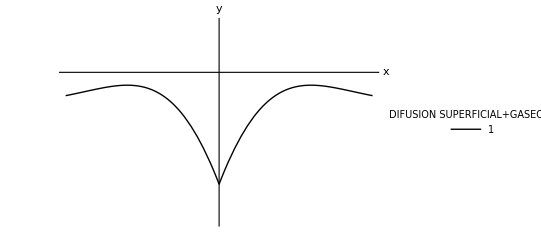

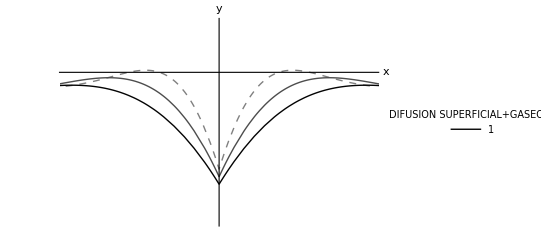

```mathematica
t=1
t2=1.5
t3=2
g1=Plot[(-0.862+Abs[x/t]+2/(3*π)*∑_(n=1)^100 ((-1)^n Gamma[(2*n-1)/3])/Factorial[(2*n)]*Abs[x/t]^(2*n))*t+(a0+a1*Abs[x/t]+a2*Abs[x/t]^2+a4*Abs[x/t]^4+a6*Abs[x/t]^6+a8*Abs[x/t]^8+a10*Abs[x/t]^10+a12*Abs[x/t]^12+a14*Abs[x/t]^14)*t-0.3*t,{x,-5,5},Frame->False,AxesLabel->{x,y},PlotRange->{-3,1},PlotStyle->{GrayLevel[.5],Dashed,Thick},Frame->True,GridLines->Automatic, AxesStyle->Directive[Black,22],Ticks->None]
g2=Plot[(-0.862+Abs[x/t2]+2/(3*π)*∑_(n=1)^100 ((-1)^n Gamma[(2*n-1)/3])/Factorial[(2*n)]*Abs[x/t2]^(2*n))*t+(a0+a1*Abs[x/t2]+a2*Abs[x/t2]^2+a4*Abs[x/t2]^4+a6*Abs[x/t2]^6+a8*Abs[x/t2]^8+a10*Abs[x/t2]^10+a12*Abs[x/t2]^12+a14*Abs[x/t2]^14)*t-0.3*t2,{x,-8,8},Frame->False,AxesLabel->{x,y},PlotRange->{-3,1},PlotStyle->{GrayLevel[.3],Thick},Frame->True,GridLines->Automatic, AxesStyle->Directive[Black,22],Ticks->None]
g3=Plot[(-0.862+Abs[x/t3]+2/(3*π)*∑_(n=1)^100 ((-1)^n Gamma[(2*n-1)/3])/Factorial[(2*n)]*Abs[x/t3]^(2*n))*t+(a0+a1*Abs[x/t3]+a2*Abs[x/t3]^2+a4*Abs[x/t3]^4+a6*Abs[x/t3]^6+a8*Abs[x/t3]^8+a10*Abs[x/t3]^10+a12*Abs[x/t3]^12+a14*Abs[x/t3]^14)*t-0.3*t3,{x,-8,8},Frame->False,AxesLabel->{x,y},PlotRange->{-3,1},PlotStyle->{GrayLevel[.01],Thick},Frame->True,GridLines->Automatic, AxesStyle->Directive[Black,22],Ticks->None,PlotLegends->LineLegend[{1,10,100,1000,10000},LegendMarkerSize->{30,10},LegendLabel->DIFUSION SUPERFICIAL+GASEOSA]]
Show[g1,g2,g3]
```

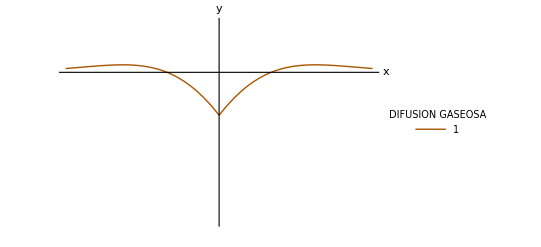

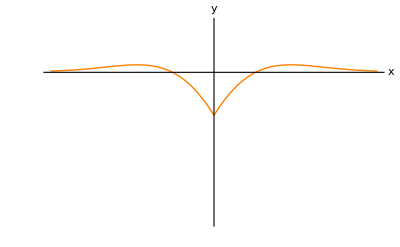

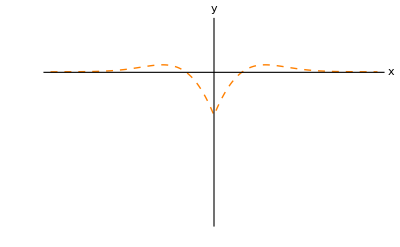

```mathematica
h3=Plot[(-0.862+Abs[x/t3]+2/(3*π)*∑_(n=1)^100 ((-1)^n Gamma[(2*n-1)/3])/Factorial[(2*n)]*Abs[x/t3]^(2*n))*t,{x,-8,8},Frame->False,AxesLabel->{x,y},PlotRange->{-3,1},PlotStyle->{Darker[Orange],Thick},Frame->True,GridLines->Automatic, AxesStyle->Directive[Black,22],Ticks->None,PlotLegends->LineLegend[{1,10,100,1000,10000},LegendMarkerSize->{30,10},LegendLabel->DIFUSION GASEOSA]]
h2=Plot[(-0.862+Abs[x/t2]+2/(3*π)*∑_(n=1)^100 ((-1)^n Gamma[(2*n-1)/3])/Factorial[(2*n)]*Abs[x/t2]^(2*n))*t,{x,-8,8},Frame->False,AxesLabel->{x,y},PlotRange->{-3,1},PlotStyle->{Orange,Thick},Frame->True,GridLines->Automatic, AxesStyle->Directive[Black,22],Ticks->None]
h1=Plot[(-0.862+Abs[x/t]+2/(3*π)*∑_(n=1)^100 ((-1)^n Gamma[(2*n-1)/3])/Factorial[(2*n)]*Abs[x/t]^(2*n))*t,{x,-8,8},Frame->False,AxesLabel->{x,y},PlotRange->{-3,1},PlotStyle->{Orange,Dashed,Thick},Frame->True,GridLines->Automatic, AxesStyle->Directive[Black,22],Ticks->None]
```

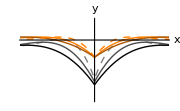

```mathematica
Show[g1,g2,g3,h2,h3,h1]
```

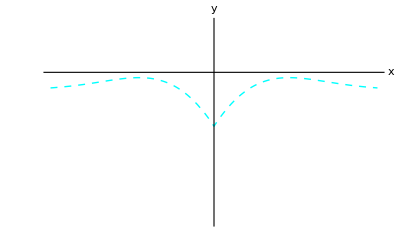

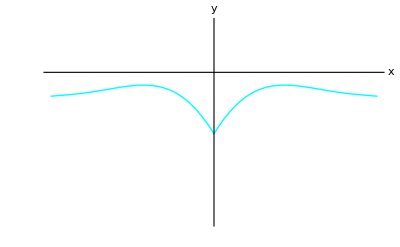

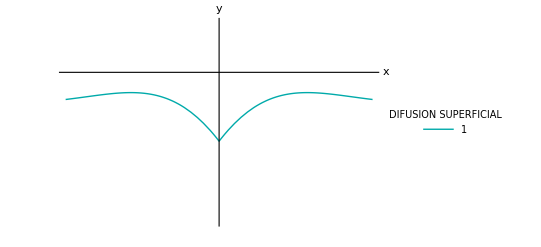

```mathematica
b1=Plot[(a0+a1*Abs[x/t]+a2*Abs[x/t]^2+a4*Abs[x/t]^4+a6*Abs[x/t]^6+a8*Abs[x/t]^8+a10*Abs[x/t]^10+a12*Abs[x/t]^12+a14*Abs[x/t]^14)*t-0.3*t,{x,-5,5},Frame->False,AxesLabel->{x,y},PlotRange->{-3,1},PlotStyle->{Cyan,Dashed,Thick},Frame->True,GridLines->Automatic, AxesStyle->Directive[Black,22],Ticks->None]
b2=Plot[(a0+a1*Abs[x/t2]+a2*Abs[x/t2]^2+a4*Abs[x/t2]^4+a6*Abs[x/t2]^6+a8*Abs[x/t2]^8+a10*Abs[x/t2]^10+a12*Abs[x/t2]^12+a14*Abs[x/t2]^14)*t-0.3*t2,{x,-8,8},Frame->False,AxesLabel->{x,y},PlotRange->{-3,1},PlotStyle->{Cyan,Thick},Frame->True,GridLines->Automatic, AxesStyle->Directive[Black,22],Ticks->None]
b3=Plot[(a0+a1*Abs[x/t3]+a2*Abs[x/t3]^2+a4*Abs[x/t3]^4+a6*Abs[x/t3]^6+a8*Abs[x/t3]^8+a10*Abs[x/t3]^10+a12*Abs[x/t3]^12+a14*Abs[x/t3]^14)*t-0.3*t3,{x,-8,8},Frame->False,AxesLabel->{x,y},PlotRange->{-3,1},PlotStyle->{Darker[Cyan],Thick},Frame->True,GridLines->Automatic, AxesStyle->Directive[Black,22],Ticks->None,PlotLegends->LineLegend[{1,10,100,1000,10000},LegendMarkerSize->{30,10},LegendLabel->DIFUSION SUPERFICIAL]]
```

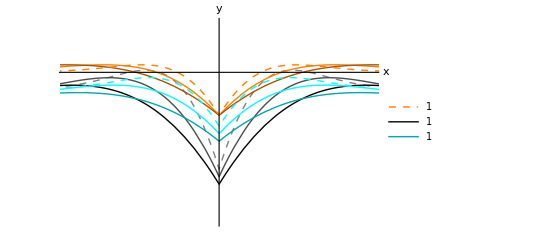

```mathematica
s=Show[g1,g2,g3,h2,h3,h1,b1,b2,b3]
```

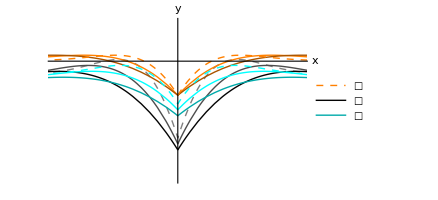

```mathematica
Export["suma.png",s]
```

suma.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["suma.png"]]]
```

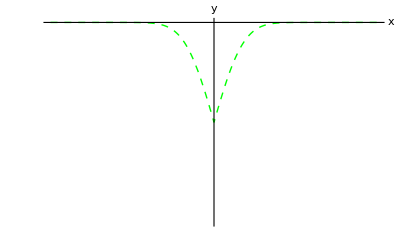

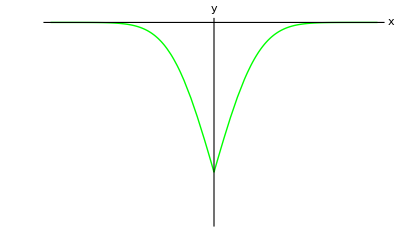

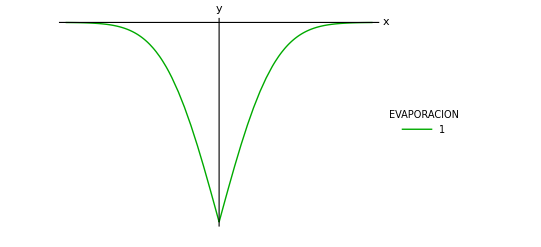

```mathematica
f1=Plot[-t*Erfc[Abs[x/t]],{x,-5,5},PlotRange->{-2,0},Frame->False,AxesLabel->{x,y},PlotStyle->{Green,Dashed,Thick},Frame->True,GridLines->Automatic, AxesStyle->Directive[Black,22],Ticks->None]
f2=Plot[-t2*Erfc[Abs[x/t2]],{x,-5,5},PlotRange->{-2,0},Frame->False,AxesLabel->{x,y},PlotStyle->{Green,Thick},Frame->True,GridLines->Automatic, AxesStyle->Directive[Black,22],Ticks->None]
f3=Plot[-t3*Erfc[Abs[x/t3]],{x,-5,5},PlotRange->{-2,0},Frame->False,AxesLabel->{x,y},PlotStyle->{Darker[Green],Thick},Frame->True,GridLines->Automatic, AxesStyle->Directive[Black,22],Ticks->None,PlotLegends->LineLegend[{1,10,100,1000,10000},LegendMarkerSize->{30,10},LegendLabel->EVAPORACION]]
```

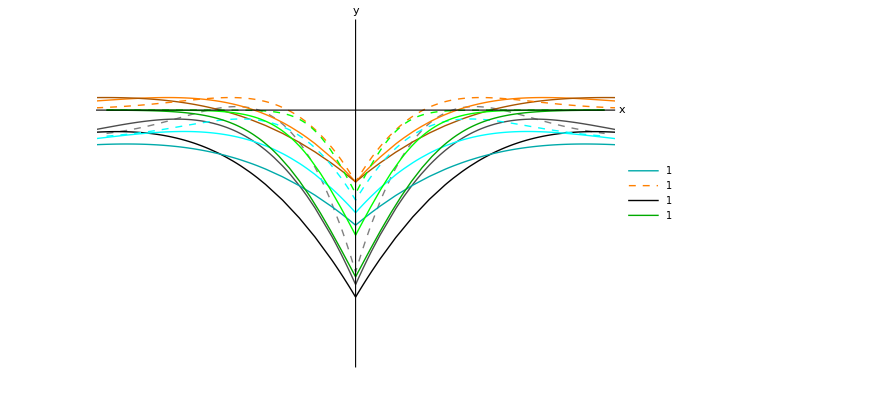

```mathematica
Show[g1,g2,g3,h2,h3,h1,b1,b2,b3,f1,f2,f3]
```

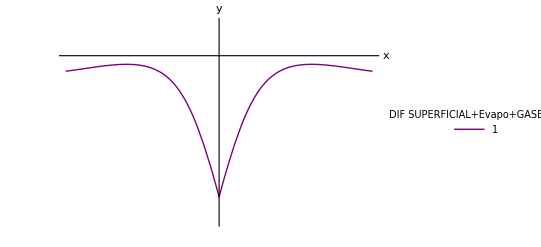

```mathematica
E3=Plot[-t3*Erfc[Abs[x/t3]]+(-0.862+Abs[x/t3]+2/(3*π)*∑_(n=1)^100 ((-1)^n Gamma[(2*n-1)/3])/Factorial[(2*n)]*Abs[x/t3]^(2*n))*t+(a0+a1*Abs[x/t3]+a2*Abs[x/t3]^2+a4*Abs[x/t3]^4+a6*Abs[x/t3]^6+a8*Abs[x/t3]^8+a10*Abs[x/t3]^10+a12*Abs[x/t3]^12+a14*Abs[x/t3]^14)*t-0.3*t3,{x,-8,8},Frame->False,AxesLabel->{x,y},PlotRange->{-5,1},PlotStyle->{Purple,Thick},Frame->True,GridLines->Automatic, AxesStyle->Directive[Black,22],Ticks->None,PlotLegends->LineLegend[{1,10,100,1000,10000},LegendMarkerSize->{30,10},LegendLabel->DIF SUPERFICIAL+GASEOSA+Evapo]]
```

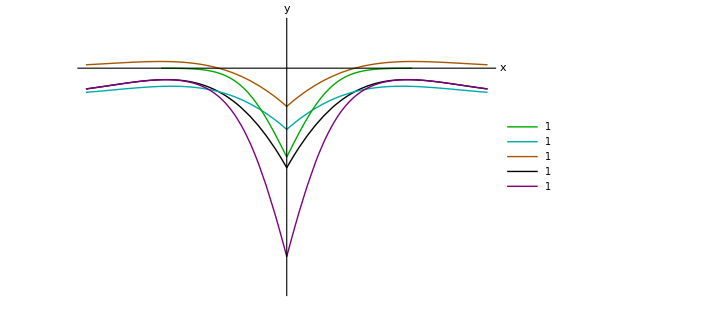

```mathematica
s2=Show[g3,h3,b3,f3,E3,PlotRange-> {-5,1}]
```

```mathematica
Export["suma2.png",s2]
```

suma2.png